```mathematica
α=0.2573
v=0.3;
```

0.2573

```mathematica
ClearAll
```

ClearAll

```mathematica
A1[z_]:=(1/2) Log[2.94 Sin[1.24 Sin[0.47 z+1.94]-9.55]+3.53]
```

```mathematica
AS1[z_]:=(1/2) Log[2.94 Sin[1.24 Sin[0.47 z+1.94]-9.55]+3.53]
```

```mathematica
T1[zh_]:=1/(π zh)
```

```mathematica
Fdrag1[zs_]:=-((α*v*Exp[2*AS1[zs]])/(2*π*zs^2));
```

```mathematica
g1[z_,zh_]:=1-(1/zh^4)z^4
```

```mathematica
getZh1[zs_]:=Module[{zh1Value},zh1Value=FindRoot[g1[zs,zh]==v^2,{zh,0.4}][[1,2]];
zh1Value];
```

```mathematica
zs1Values=Range[0.3,10,0.1];
```

```mathematica
fdrag1Values=-Fdrag1/@zs1Values;
zh1Values=getZh1/@zs1Values;
t1Values=T1/@zh1Values;
```

```mathematica
ListLinePlot[Transpose[{t3Values,zh2Values}],PlotStyle->{Red,Thick},(*设置线条的颜色和粗细*)AxesLabel->{"T","zh"},PlotLabel->"zh 与 T ",(*设置图像标题*)GridLines->Automatic,(*添加网格线*)PlotRange->{{0,0.7},Automatic} ]
```

```mathematica
t1=ListLinePlot[Transpose[{t1Values,fdrag1Values}],Frame->True,PlotStyle->{Black,Thickness[0.005]},(*设置线条颜色和粗细*)PlotLegends->Placed[LineLegend[{"μ=0"}],{0.6,0.9}],(*图例字体保持不变*)FrameLabel->{Style["T",15,Black,Italic,"Times New Roman"],Style["\!\(\*SubscriptBox[\(F\), \(drag\)]\)",15,Black,"Times New Roman"]},FrameStyle->Directive[Black,FontSize->15,FontFamily->"Times New Roman"],PlotRange->{{0.01,0.7},{0,0.08}},ImageSize->{500,300}]
```

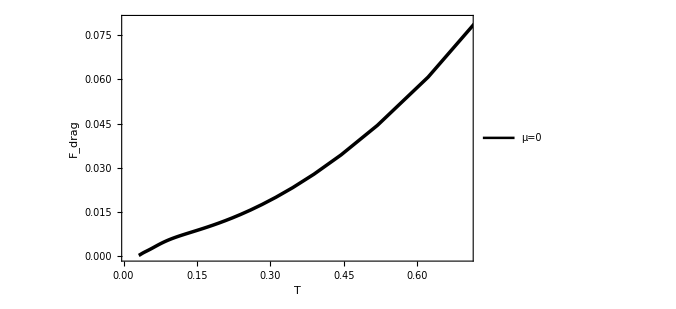

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.